```mathematica
E2[n_,k_]:=Sum[(-1)^j E2[n/j,k-1],{j,2,n}];E2[n_,0]:=1
P2[ n_] := Sum[ k^-1 E2[ n,k],{k,1,Log[2,n]}]
```

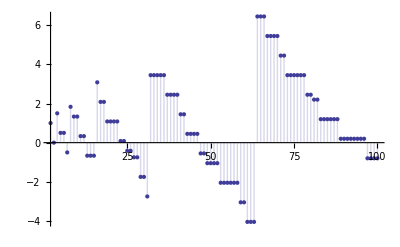

```mathematica
DiscretePlot[ P2[n],{n,2,100}]
```

```mathematica
E2[1000,5]
```

-190

```mathematica
eee[n_, 0, a_] := 1
eee[n_,k_,a_]:=If[n<a^k,0,Sum[Binomial[k,j] ((-1)^(a+1))^j eee[n/a^j,k-j,a+1],{j,0,k}]]
```

```mathematica
eee[1000,5,2]
```

190

```mathematica
ee3[n_, 0, a_] := 1
ee3[n_,k_,a_]:=Sum[Binomial[k,j] ((-1)^m)^j ee3[n/((m)^j),k-j,m],{j,1,k},{m,a+1,Floor[n^(1/k)]}]
ee3[10000,5,1]
```

-1139

```mathematica
ee4[n_, 0, a_] := 1
ee4[n_, 1, a_] := -1/2 (-1)^a+1/2 (-1)^Floor[n]
ee4[n_,k_,a_]:=Sum[((-1)^m)^k ,{m,a+1,Floor[n^(1/k)]}]+Sum[Binomial[k,j] ((-1)^m)^j ee4[n/(m^j),k-j,m],{m,a+1,Floor[n^(1/k)]},{j,1,k-1}]
ee4[1000,5,1]
```

-190

```mathematica
ee5[n_, 0, a_] := 1
ee5[n_, 1, a_] := -1/2 (-1)^a+1/2 (-1)^Floor[n]
ee5[n_,k_,a_]:=Sum[((-1)^m)^k ,{m,a+1,Floor[n^(1/k)]}]+
Sum[k ((-1)^m)^(k-1) ee5[n/(m^(k-1)),1,m],{m,a+1,Floor[n^(1/k)]}]+
Sum[Binomial[k,j] ((-1)^m)^j ee5[n/(m^j),k-j,m],{m,a+1,Floor[n^(1/k)]},{j,1,k-2}]
ee5[10000,5,1]
```

-1139

```mathematica
ee6[n_, 0, a_] := 1
ee6[n_, 1, a_] := -1/2 (-1)^a+1/2 (-1)^Floor[n]
ee6[n_,2_,a_]:=Sum[((-1)^m)^2 ,{m,a+1,Floor[n^(1/2)]}]+
2 Sum[ ((-1)^m)^(2-1) (-1/2 (-1)^m+1/2 (-1)^Floor[n/(m^(2-1))]),{m,a+1,Floor[n^(1/2)]}]
ee6[n_,k_,a_]:=Sum[((-1)^m)^k ,{m,a+1,Floor[n^(1/k)]}]+
k Sum[ ((-1)^m)^(k-1) (-1/2 (-1)^m+1/2 (-1)^Floor[n/(m^(k-1))]),{m,a+1,Floor[n^(1/k)]}]+
Sum[Binomial[k,j] ((-1)^m)^j ee6[n/(m^j),k-j,m],{m,a+1,Floor[n^(1/k)]},{j,1,k-2}]
ee6[10000,5,1]
```

-1139

```mathematica
Sum[((-1)^m)^k ,{m,a+1,Floor[n^(1/k)]}]+
k Sum[ ((-1)^m)^(k-1) (-1/2 (-1)^m+1/2 (-1)^Floor[n/(m^(k-1))]),{m,a+1,Floor[n^(1/k)]}]
```

$Aborted

```mathematica
ee7[n_, 0, a_] := 1
ee7[n_, 1, a_] := -1/2 (-1)^a+1/2 (-1)^Floor[n]
ee7[n_,2,a_]:=Sum[((-1)^m)^2 ,{m,a+1,Floor[n^(1/2)]}]+
2 Sum[ ((-1)^m)^(2-1) (-1/2 (-1)^m+1/2 (-1)^Floor[n/(m^(2-1))]),{m,a+1,Floor[n^(1/2)]}]
ee7[n_,k_,a_]:=Sum[((-1)^m)^k ,{m,a+1,Floor[n^(1/k)]}]+
k Sum[ ((-1)^m)^(k-1) (-1/2 (-1)^m+1/2 (-1)^Floor[n/(m^(k-1))]),{m,a+1,Floor[n^(1/k)]}]+
Sum[Binomial[k,j] ((-1)^m)^j ee7[n/(m^j),k-j,m],{m,a+1,Floor[n^(1/k)]},{j,1,k-2}]
ee7[10000,5,1]
```

-1139

```mathematica
Sum[((-1)^m)^2 ,{m,a+1,Floor[n^(1/2)]}]+
2 Sum[ ((-1)^m) (-1/2 (-1)^m+1/2 (-1)^Floor[n/(m^(2-1))]),{m,a+1,Floor[n^(1/2)]}]
```

$Aborted

```mathematica
Sum[((-1)^m)^2 ,{m,a+1,Floor[n^(1/2)]}]
```

(-1)^(2 Floor[√n]) (-a+Floor[√n])

```mathematica
2 Sum[ ((-1)^m) (-1/2 (-1)^m+1/2 (-1)^Floor[n/m]),{m,a+1,Floor[n^(1/2)]}]
```

```mathematica
Expand[((-1)^m) (-1/2 (-1)^m+1/2 (-1)^Floor[n/m])]
```

-1/2 (-1)^(2 m)+1/2 (-1)^(m+Floor[n/m])

```mathematica
2 Sum[ -1/2 (-1)^(2 m)+1/2 (-1)^(m+Floor[n/m]),{m,a+1,Floor[n^(1/2)]}]
```

2 ∑_(m=1+a)^Floor[√n] (-1/2 (-1)^(2 m)+1/2 (-1)^(m+Floor[n/m]))

```mathematica
2 Sum[ -1/2 (-1)^(2 m),{m,a+1,Floor[n^(1/2)]}]
2 Sum[ 1/2 (-1)^(m+Floor[n/m]),{m,a+1,Floor[n^(1/2)]}]
```

(-1)^(2 Floor[√n]) (a-Floor[√n])

2 ∑_(m=1+a)^Floor[√n] 1/2 (-1)^(m+Floor[n/m])

```mathematica
FullSimplify[(-1)^(2 Floor[√n]) (-a+Floor[√n]) + (-1)^(2 Floor[√n]) (a-Floor[√n]) + 2 ∑_(m=1+a)^Floor[√n] 1/2 (-1)^(m+Floor[n/m])]
```

2 ∑_(m=1+a)^Floor[√n] 1/2 (-1)^(m+Floor[n/m])

```mathematica
ee8[n_, 0, a_] := 1
ee8[n_, 1, a_] := -1/2 (-1)^a+1/2 (-1)^Floor[n]
ee8[n_,2,a_]:=∑_(m=1+a)^Floor[√n] (-1)^(m+Floor[n/m])
ee8[n_,k_,a_]:=Sum[((-1)^m)^k ,{m,a+1,Floor[n^(1/k)]}]+
k Sum[ ((-1)^m)^(k-1) (-1/2 (-1)^m+1/2 (-1)^Floor[n/(m^(k-1))]),{m,a+1,Floor[n^(1/k)]}]+
Sum[Binomial[k,j] ((-1)^m)^j ee8[n/(m^j),k-j,m],{m,a+1,Floor[n^(1/k)]},{j,1,k-2}]
ee8[10000,5,1]
```

-1139

```mathematica
ee9[n_, 0, a_] := 1
ee9[n_, 1, a_] := -1/2 (-1)^a+1/2 (-1)^Floor[n]
ee9[n2_,2,a2_]:=∑_(m2=1+a2)^Floor[√n2] (-1)^(m2+Floor[n2/m2])
ee9[n_,k_,a_]:=Sum[((-1)^m)^k ,{m,a+1,Floor[n^(1/k)]}]+
k Sum[ ((-1)^m)^(k-1) (-1/2 (-1)^m+1/2 (-1)^Floor[n/(m^(k-1))]),{m,a+1,Floor[n^(1/k)]}]+
(1/2 (-1+k) k)Sum[ ((-1)^m)^(k-2)( ∑_(m2=1+m)^Floor[√(n/(m^(k-2)))] (-1)^(m2+Floor[(n/(m^(k-2)))/m2])),{m,a+1,Floor[n^(1/k)]}]+
Sum[Binomial[k,j] ((-1)^m)^j ee9[n/(m^j),k-j,m],{m,a+1,Floor[n^(1/k)]},{j,1,k-3}]
ee9[10000,5,1]
```

-1139

```mathematica
ee9a[n_, 0, a_] := 1
ee9a[n_, 1, a_] := -1/2 (-1)^a+1/2 (-1)^Floor[n]
ee9a[n2_,2,a2_]:=∑_(m2=1+a2)^Floor[√n2] (-1)^(m2+Floor[n2/m2])
ee9a[n_, 3, a_] := Sum[((-1)^m)^3 ,{m,a+1,Floor[n^(1/3)]}]+
3 Sum[ ((-1)^m)^2 (-1/2 (-1)^m+1/2 (-1)^Floor[n/(m^2)]),{m,a+1,Floor[n^(1/3)]}]+
3Sum[ ((-1)^m)( ∑_(m2=1+m)^Floor[√(n/m)] (-1)^(m2+Floor[(n/m)/m2])),{m,a+1,Floor[n^(1/3)]}]
ee9a[n_,k_,a_]:=Sum[((-1)^m)^k ,{m,a+1,Floor[n^(1/k)]}]+
k Sum[ ((-1)^m)^(k-1) (-1/2 (-1)^m+1/2 (-1)^Floor[n/(m^(k-1))]),{m,a+1,Floor[n^(1/k)]}]+
(1/2 (-1+k) k)Sum[ ((-1)^m)^(k-2)( ∑_(m2=1+m)^Floor[√(n/(m^(k-2)))] (-1)^(m2+Floor[(n/(m^(k-2)))/m2])),{m,a+1,Floor[n^(1/k)]}]+
Sum[Binomial[k,j] ((-1)^m)^j ee9a[n/(m^j),k-j,m],{m,a+1,Floor[n^(1/k)]},{j,1,k-3}]
ee9a[10000,5,1]
```

-1139

```mathematica
ee9a[n_, 0, a_] := 1
ee9a[n_, 1, a_] := -1/2 (-1)^a+1/2 (-1)^Floor[n]
ee9b[n2_,2,a2_]:=∑_(m2=1+a2)^Floor[√n2] (-1)^(m2+Floor[n2/m2])
ee9b[n_, 3, a_] := (1/2 (-(-1)^(3 a)+(-1)^(3 Floor[n^(1/3)])))+
(3/4 ((-1)^a-(-1)^Floor[n^(1/3)]))+
3/2 ∑_(m=1+a)^Floor[n^(1/3)] (-1)^Floor[n/m^2]+
3Sum[ ((-1)^m)( ∑_(m2=1+m)^Floor[√(n/m)] (-1)^(m2+Floor[(n/m)/m2])),{m,a+1,Floor[n^(1/3)]}]
ee9b[n_,k_,a_]:=Sum[((-1)^m)^k ,{m,a+1,Floor[n^(1/k)]}]+
k Sum[ ((-1)^m)^(k-1) (-1/2 (-1)^m+1/2 (-1)^Floor[n/(m^(k-1))]),{m,a+1,Floor[n^(1/k)]}]+
(1/2 (-1+k) k)Sum[ ((-1)^m)^(k-2)( ∑_(m2=1+m)^Floor[√(n/(m^(k-2)))] (-1)^(m2+Floor[(n/(m^(k-2)))/m2])),{m,a+1,Floor[n^(1/k)]}]+
Sum[Binomial[k,j] ((-1)^m)^j ee9b[n/(m^j),k-j,m],{m,a+1,Floor[n^(1/k)]},{j,1,k-3}]
ee9b[10000,5,1]
```

-1139